```mathematica
libraryPath=StringJoin[NotebookDirectory[],"../../Mathematica/CESDSOL.wl"];
outputPath=StringJoin[NotebookDirectory[],"output/"];
Import[libraryPath];
```

```mathematica
CESDSOL`StationaryProblem[{
{
phi''[x]-g Sin[phi[x]],
Left[x]->phi[x]-π,
Right[x]->phi[x]-2π
}
},
{phi},
{x},
DirectProductGrid[UniformRange[0,10,1000]],
Parameters->{g},
Name->"StaticSineGordon"]
```

auto descriptor = StationaryProblemDescriptor<1, double, double>(GridDescriptor<1, double>(3), Array<Array<std::array<size_t, 1>>>{{{2}}}, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0);
descriptor.SetProblemName("StaticSineGordon");
descriptor.SetParameterName(0, "g");
descriptor.SetVariableName(0, "phi");
descriptor.SetContinuousEquation(0, 0, [](const auto& l, const auto& g) {return -(g.Parameters[0]*sin(l.FieldValues[0])) + l.DerivativeValues[0][0];});
descriptor.SetContinuousEquation(0, 1, [](const auto& l, const auto& g) {return -Pi + l.FieldValues[0];});
descriptor.SetContinuousEquation(0, 2, [](const auto& l, const auto& g) {return -2*Pi + l.FieldValues[0];});
descriptor.SetJacobianComponent(0, 0, 0, 0, [](const auto& l, const auto& g) {return -(g.Parameters[0]*cos(l.FieldValues[0]));});
descriptor.SetJacobianComponent(0, 0, 1, 0, [](const auto& l, const auto& g) {return 1;});
descriptor.SetJacobianComponent(0, 0, 0, 1, [](const auto& l, const auto& g) {return 1;});
descriptor.SetJacobianComponent(0, 0, 0, 2, [](const auto& l, const auto& g) {return 1;});
auto grid = std::make_shared<DirectProductGrid<1, double>>(SingleDimensionalGrid<double>({MakeUniformRange<double>(0, 10, 1000), std::nullopt}));
std::unique_ptr<Discretization<1>> discretization = std::make_unique<StructuredFiniteDifferenceDiscretization<1>>(5);
auto problem = descriptor.MakeProblem(grid, std::move(discretization));

```mathematica
solutions=ReadSolution/@FileNames["StaticSineGordon_g=*.dat",outputPath];
```

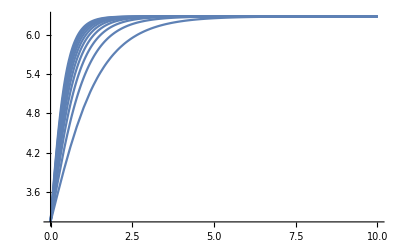

```mathematica
Plot[#["phi"][x]&/@solutions,{x,0,10},PlotRange->All]
```